```mathematica
Solve[x+2z== 2&&x+3y+z==2&&2y+z==1,{x,y,z}]
```

{{x→4/5,y→1/5,z→3/5}}

```mathematica
%*6.242*^18
```

```mathematica
(*calculating velocity of α*)
u=1.660539040*^-27;
m0=211.9888421*u;
m1=207.9766521*u;
m2=4.002602*u;
en=(m0-m1-m2)*299792458^2
NSolve[m1*v1+m2*v2==0&&m1*v1^2/2 +m2*v2^2/2==en,{v1,v2}]
```

1.43093×10^-12

{{v1→-395564.,v2→2.05537×10^7},{v1→395564.,v2→-2.05537×10^7}}

```mathematica
m2(2.055365777143917*^7)^2/2
```

1.40391×10^-12

```mathematica
(*Calculating radius of potential well*)
1.4*^-15*(208)^(1/3)
```

8.29499×10^-15

```mathematica
Clear[x]
```

8.85419×10^-12

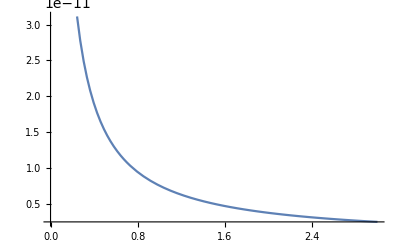

```mathematica
(*Coulomb potential*)
Z1=2;
Z2=84-2;
echarge=1.602176620*^-19;
ϵ0=8.854187817*^-12
Plot[2Z1*Z2*echarge^2/(4Pi*ϵ0 r),{r,0,3*^-14}]
```

```mathematica
Solve[a1 b1^2/2 + a2 b2^2/2==Ek&&a1 b1+a2 b2==0,{b1,b2}]
FullSimplify@%
```

{{b1→-(√2 √a2 √Ek)/(√(a1^2+a1 a2)),b2→(√2 a1 √Ek)/(√a2 √(a1 (a1+a2)))},{b1→(√2 √a2 √Ek)/(√(a1^2+a1 a2)),b2→-(√2 a1 √Ek)/(√a2 √(a1 (a1+a2)))}}

{{b1→-(√2 √a2 √Ek)/(√(a1 (a1+a2))),b2→(√2 a1 √Ek)/(√a2 √(a1 (a1+a2)))},{b1→(√2 √a2 √Ek)/(√(a1 (a1+a2))),b2→-(√2 a1 √Ek)/(√a2 √(a1 (a1+a2)))}}

```mathematica
segments=120;

u=1.660539040*^-27;
m0=211.9888421*u;
m1=207.9766521*u;
m2=4.002602*u;
en=(m0-m1-m2)*299792458^2;
v=NSolve[m1*v1+m2*v2==0&&m1*v1^2/2 +m2*v2^2/2==en,{v1,v2}][[1]][[2]][[2]];

ek=v^2*m2/2;

Z1=2;
Z2=84-2;
echarge=1.602176620*^-19;
ϵ0=8.854187817*^-12;
V[r_]=Z1 Z2 echarge^2/(4Pi ϵ0 r);

hbar=1.0545718*^-34;
V0=2.14692*^-11;

cr=1.4*^-15;
r0=(212)^(1/3)cr;

k0=Sqrt[2m2(ek-V[r0]+V0)]/hbar;
k[r_]=Sqrt[2m2(ek-V[r])]/hbar;

rmax=Z1 Z2 echarge^2/(4Pi ϵ0 ek);
stepsize=(rmax-r0)/segments;

klist={};
AppendTo[klist,k0];
ktable=Table[k[r-0.5stepsize],{r,r0,rmax,stepsize}];
klist=Join[klist,ktable];
klist[[Length[klist]]]=k0; (*fishy stuff*)
Length[klist];

odd=Table[{Exp[I klist[[i]] (r0+(i-1)stepsize)],
Exp[-I klist[[i]] (r0+(i-1)stepsize)],
-Exp[I klist[[i+1]] (r0+(i-1)stepsize)],
-Exp[-I klist[[i+1]] (r0+(i-1)stepsize)]},{i,1,(segments)+1,1}];

even=Table[{I klist[[i]]Exp[I klist[[i]] (r0+(i-1)stepsize)],
-I klist[[i]]Exp[-I klist[[i]] (r0+(i-1)stepsize)],
-I klist[[i+1]]Exp[I klist[[i+1]] (r0+(i-1)stepsize)],
I klist[[i+1]]Exp[-I klist[[i+1]] (r0+(i-1)stepsize)]},{i,1,(segments+1),1}];

sch=ConstantArray[0,{2(segments+1),2(segments+1)+2}];

For[i=1,i<=(segments+1),i++,{sch[[1+(i-1)2]][[1+2(i-1)]]=odd[[i]][[1]],sch[[1+(i-1)2]][[2+2(i-1)]]=odd[[i]][[2]],sch[[1+(i-1)2]][[3+2(i-1)]]=odd[[i]][[3]],sch[[1+(i-1)2]][[4+2(i-1)]]=odd[[i]][[4]],sch[[2i]][[1+2(i-1)]]=even[[i]][[1]],sch[[2i]][[2+2(i-1)]]=even[[i]][[2]],sch[[2i]][[3+2(i-1)]]=even[[i]][[3]],sch[[2i]][[4+2(i-1)]]=even[[i]][[4]]}]

sch[[2(segments+1)]][[2(segments+1)+2]]=0;
sch[[2(segments+1)-1]][[2(segments+1)+2]]=0;

top=ConstantArray[0,{1,2(segments+1)+2}];
top[[1]][[1]]=1;
sch=Join[top,sch];

bot=ConstantArray[0,{1,2(segments+1)+2}][[1]];
bot[[Length[bot]]]=1;
AppendTo[sch,bot];

sch;
B=top[[1]];

isch=Inverse[sch];

(*sch={{1,0,0,0,0,0,0,0,0,0},
{odd[[1]][[1]],odd[[1]][[2]],odd[[1]][[3]],odd[[1]][[4]],0,0,0,0,0,0},
{even[[1]][[1]],even[[1]][[2]],even[[1]][[3]],even[[1]][[4]],0,0,0,0,0,0},{0,0,odd[[2]][[1]],odd[[2]][[2]],odd[[2]][[3]],odd[[2]][[4]],0,0,0,0},
{0,0,even[[2]][[1]],even[[2]][[2]],even[[2]][[3]],even[[2]][[4]],0,0,0,0},{0,0,0,0,odd[[3]][[1]],odd[[3]][[2]],odd[[3]][[3]],odd[[3]][[4]],0,0},
{0,0,0,0,even[[3]][[1]],even[[3]][[2]],even[[3]][[3]],even[[3]][[4]],0,0},{0,0,0,0,0,0,odd[[4]][[1]],odd[[4]][[2]],odd[[4]][[3]],0},
{0,0,0,0,0,0,even[[4]][[1]],even[[4]][[2]],even[[4]][[3]],0},
{0,0,0,0,0,0,0,0,0,1}};*)


sols1=isch.B;
sols2=LinearSolve[sch,B];

Abs[sols1[[Length[B]-1]]]^2
T=Abs[sols2[[Length[B]-1]]]^2

hits=v/(2r0);

Log[2]/(hits T)
```

Inverse::luc: Result for Inverse of badly conditioned matrix … may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix … may contain significant numerical errors.

0.0416145

0.0416145

1.35299×10^-20

```mathematica
{1.+1.2891194584903142*^-16 ⅈ,-0.9609027185273306-0.18722039315784705 ⅈ,1.0633955454593969+0.660372210255733 ⅈ,-1.0129801590051466+0.2677287230334668 ⅈ,1.0633955454593969+0.6603722102557329 ⅈ,-1.0129801590051466+0.2677287230334667 ⅈ,1.0633955454593969+0.6603722102557328 ⅈ,-1.0129801590051466+0.2677287230334666 ⅈ,1.0633955454593969+0.6603722102557328 ⅈ,-1.0129801590051466+0.2677287230334666 ⅈ,1.0633955454593969+0.6603722102557329 ⅈ,-1.0129801590051466+0.2677287230334666 ⅈ,0.05173364554750197+0.19732744317750778 ⅈ,0.+0. ⅈ}
```

```mathematica
Exp[-I klist[[1]] (r0+(1-1)stepsize)]
```

0.0437481+0.999043 ⅈ

```mathematica
A={{+1.000*^+00+0.000*^+00,0+0,0+0,0+0,0+0,0+0,0+0,0+0,0+0,0+0},{+4.461*^-01+8.950*^-01 I,+4.461*^-01+-8.950*^-01 I,-2.929*^-10+-0.000*^+00,-3.414*^+09+0.000*^+00,0+0,0+0,0+0,0+0,0+0,0+0},{-4.187*^+15+2.087*^+15 I,-4.187*^+15 +-2.087*^+15 I,+4.431*^+05+0.000*^+00,-5.163*^+24+0.000*^+00,0+0,0+0,0+0,0+0,0+0,0+0},{0+0,0+0,+2.929*^-10+0.000*^+00,+3.414*^+09+-0.000*^+00,-3.269*^-09+-0.000*^+00,-3.059*^+08+0.000*^+00,0+0,0+0,0+0,0+0},{0+0,0+0,-4.431*^+05+0.000*^+00,+5.163*^+24+-0.000*^+00,+3.081*^+06+0.000*^+00,-2.883*^+23+0.000*^+00,0+0,0+0,0+0,0+0},{0+0,0+0,0+0,0+0,+3.269*^-09+0.000*^+00,+3.059*^+08+-0.000*^+00,-3.346*^-06+-0.000*^+00,-2.988*^+05+0.000*^+00,0+0,0+0},{0+0,0+0,0+0,0+0,-3.081*^+06+0.000*^+00,+2.883*^+23+-0.000*^+00,+1.565*^+09+0.000*^+00,-1.398*^+20+0.000*^+00,0+0,0+0},{0+0,0+0,0+0,0+0,0+0,0+0,+3.346*^-06+0.000*^+00,+2.988*^+05+-0.000*^+00,-5.275*^-01+8.496*^-01 I,0+0},{0+0,0+0,0+0,0+0,0+0,0+0,-1.565*^+09+0.000*^+00,+1.398*^+20+-0.000*^+00,-1.101*^+15+-6.833*^+14 I,0+0},{0+0,0+0,0+0,0+0,0+0,0+0,0+0,0+0,0+0,+1.000*^+00+0.000*^+00}};
A//MatrixForm

AI = Inverse[A];

B={1,0,0,0,0,0,0,0,0,0};

sols1=LinearSolve[A,B]  
sols2=AI.B

(Abs[sols1[[Length[sols]-1]]])^2

A.sols1-B
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4461+0.895 ⅈ | 0.4461-0.895 ⅈ | -2.929×10^-10 | -3.414×10^9 | 0 | 0 | 0 | 0 | 0 | 0
-4.187×10^15+2.087×10^15 ⅈ | -4.187×10^15-2.087×10^15 ⅈ | 443100. | -5.163×10^24 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2.929×10^-10 | 3.414×10^9 | -3.269×10^-9 | -3.059×10^8 | 0 | 0 | 0 | 0
0 | 0 | -443100. | 5.163×10^24 | 3.081×10^6 | -2.883×10^23 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3.269×10^-9 | 3.059×10^8 | -3.346×10^-6 | -298800. | 0 | 0
0 | 0 | 0 | 0 | -3.081×10^6 | 2.883×10^23 | 1.565×10^9 | -1.398×10^20 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3.346×10^-6 | 298800. | -0.5275+0.8496 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.565×10^9 | 1.398×10^20 | -1.101×10^15-6.833×10^14 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.4461+0.895 ⅈ,0.4461-0.895 ⅈ,-2.929×10^-10+0. ⅈ,-3.414×10^9+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«7»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.4461+0.895 ⅈ,0.4461-0.895 ⅈ,-2.929×10^-10+0. ⅈ,-3.414×10^9+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«7»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}} may contain significant numerical errors.

{1.-4.81269×10^-17 ⅈ,-0.340897+0.452078 ⅈ,3.24216×10^9+1.37046×10^9 ⅈ,-7.35189×10^-11+2.93019×10^-10 ⅈ,4.01599×10^8+6.74337×10^7 ⅈ,-2.00782×10^-9+3.86183×10^-9 ⅈ,684572.-79780.3 ⅈ,-5.32778×10^-6+5.58474×10^-6 ⅈ,-0.822354+1.33289 ⅈ,0.+0. ⅈ}

{1.+1.66533×10^-16 ⅈ,-0.340897+0.452078 ⅈ,3.24216×10^9+1.37046×10^9 ⅈ,-7.35189×10^-11+2.93019×10^-10 ⅈ,4.01599×10^8+6.74337×10^7 ⅈ,-2.00782×10^-9+3.86183×10^-9 ⅈ,684572.-79780.3 ⅈ,-5.32778×10^-6+5.58474×10^-6 ⅈ,-0.822354+1.33289 ⅈ,0.+0. ⅈ}

2.45288

{2.22045×10^-16-4.81269×10^-17 ⅈ,-5.55112×10^-17+0. ⅈ,0.+0. ⅈ,1.11022×10^-16-2.22045×10^-16 ⅈ,-0.125+0. ⅈ,2.22045×10^-16+4.44089×10^-16 ⅈ,-0.25+0. ⅈ,0.-4.44089×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
hbar=1.0545718*^-34;
V0=2.14692*^-11;
k0=Sqrt[2m2(1.4039115433934523*^-12+V0-Z1*Z2*echarge^2/(4Pi*ϵ0 *8.29499*^-15))]/hbar
Exp[I*k0*8.29499*^-15]
I k0 Exp[I k0 8.29499*^-15]
```

4.67843×10^15

0.446084+0.894991 ⅈ

-4.18715×10^15+2.08697×10^15 ⅈ